```mathematica
(*rotation matrix*)
rot[th_] :=({{1, 0, 0, 0}, {0, Cos[2 th], Sin[2th], 0}, {0, -Sin[2 th], Cos[2th], 0}, {0, 0, 0, 1}})
(*waveplate matrix*)
wp[th_] :=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[th], Sin[th]}, {0, 0, -Sin[th], Cos[th]}})
(*polariser matrix*)
pol := 1/2({{1, 1, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})
```

```mathematica
(*qwp at 45deg, displacer at 90deg and final polariser at 45deg. Get s0 component with [[1]]*)
FullSimplify[(pol.rot[-π/4].wp[ϕ].rot[π/4].wp[π/2].rot[π/4].{s0,s1,s2,s3})[[1]]]
```

1/2 (s0+s2 Cos[ϕ]-s1 Sin[ϕ])

```mathematica
(*Use different representation of Stokes vector - includes quarter wave plate which knocks S3 into linearly polarised light. THis is essentially I as a function of lambda, need to integrate over lambda 
to get the contrast (Apply phase delay as some exp(iphi) (ie. take the fourier transform of the spectrum) and take the real part(absolute values) of the sum of the intensities. *)
FullSimplify[(pol.rot[-π/4].wp[ϕ].rot[π/4].wp[π/2].rot[π/4].{1,Cos[2θ],Sin[2θ],0})[[1]]]
```

1/2 (1+Sin[2 θ-ϕ])

```mathematica
(*What happens without the quarter waveplate displacer at 90deg and final polariser at 45deg. Get s0 component with [[1]]*)
FullSimplify[(pol.rot[-π/4].wp[ϕ].rot[π/2].{s0,s1,s2,s3})[[1]]]
```

1/2 (s0+s2 Cos[ϕ]-s3 Sin[ϕ])

```mathematica
rot[a].rot[b]//Simplify//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[2 (a+b)] | Sin[2 (a+b)] | 0
0 | -Sin[2 (a+b)] | Cos[2 (a+b)] | 0
0 | 0 | 0 | 1)

```mathematica
(*Example of the conventional system - pem1 at 45deg, pem2 at 90deg and final polariser at 67.5deg. Get s0 component with [[1]]*)
FullSimplify[(pol.rot[-π/8].wp[δ2].rot[π/4].wp[δ1].rot[π/4].{s0,s1,s2,s3})[[1]]]
```

1/4 (2 s0-√2 (-s2 Cos[δ2]+Sin[δ1] (-s3+s1 Sin[δ2])+Cos[δ1] (s1+s3 Sin[δ2])))

```mathematica
(*A\SH Savart at 45deg, \disp at 90deg and final polariser at 45deg. Get s0 component with [[1]]. Intrinsically dependent on S3 due to using two spatial carriers, get sum and difference of the carriers*)
FullSimplify[(rot[-π/4].pol.rot[-π/4].wp[ϕD].rot[-π/4].wp[ϕS2].rot[π/2].wp[ϕS1].rot[π/4].{s0,s1,s2,s3})[[1]]]
TrigReduce[%]
```

1/2 (s0+s2 Cos[ϕD]-Sin[ϕD] (s3 Cos[ϕS1-ϕS2]+s1 Sin[ϕS1-ϕS2]))

1/4 (2 s0+2 s2 Cos[ϕD]+s1 Cos[ϕD+ϕS1-ϕS2]-s1 Cos[ϕD-ϕS1+ϕS2]-s3 Sin[ϕD+ϕS1-ϕS2]-s3 Sin[ϕD-ϕS1+ϕS2])

```mathematica
(*FLC system*)
FullSimplify[(pol.rot[-π/4].wp[ϕ+π].rot[π/4].wp[π/2].rot[π/4].{s0,s1,s2,s3})[[1]]]
FullSimplify[(pol.rot[-π/4].wp[ϕ+π].rot[π/4].wp[π+π/2].rot[π/4].{s0,s1,s2,s3})[[1]]]
```

1/2 (s0-s2 Cos[ϕ]+s1 Sin[ϕ])

1/2 (s0-s2 Cos[ϕ]-s1 Sin[ϕ])

```mathematica
(*FLC - If retardance of FLC is not precisely pi, but with some offset, can introduce some S3 component into one image. So if S3 is substantial then changes polarisation angle measurement.*)
FullSimplify[(pol.rot[-π/4].wp[ϕ+π+flcoffset].rot[π/4].wp[π/2].rot[π/4].{s0,s1,s2,s3})[[1]]]
FullSimplify[(pol.rot[-π/4].wp[ϕ+π].rot[π/4].wp[flcoffset+π/2].rot[π/4].{s0,s1,s2,s3})[[1]]]
```

1/2 (s0-s2 Cos[flcoffset+ϕ]+s1 Sin[flcoffset+ϕ])

1/2 (s0-s2 Cos[ϕ]+s1 Cos[flcoffset] Sin[ϕ]-s3 Sin[flcoffset] Sin[ϕ])

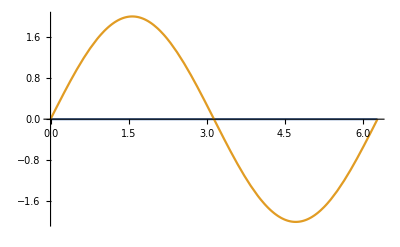

```mathematica
(* Visual representation of line broadening manifesting as contrast reduction (a represents some broadening). Adding many sine waves with slightly different phases, which reduces the contrast as seen in graph below*)
Plot[{(Sin[ϕ+a]+Sin[ϕ-a])/.a->π/2,2Sin[ϕ]},{ϕ,0,2π}]
```

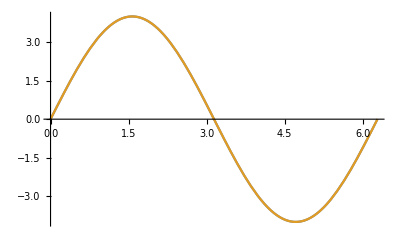

```mathematica
(* Visual representation of line broadening manifesting as contrast reduction (a represents some broadening). Adding many sine waves with slightly different phases, which reduces the contrast as seen in graph below - Example of -pi, sigma and +pi - essentially set a so that you constructively add the pi and sigma components.*)
Plot[{(-Sin[ϕ+a]+2Sin[ϕ]-Sin[ϕ-a])/.a->π,4Sin[ϕ]},{ϕ,0,2π}]
```

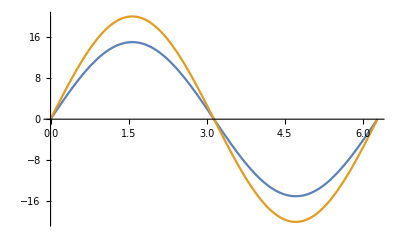

```mathematica
(* Visual representation of line broadening manifesting as contrast reduction (a represents some broadening). Adding many sine waves with slightly different phases, which reduces the contrast as seen in graph below - Example of -pi, sigma and +pi - essentially set a so that you constructively add the pi and sigma components. Showing 
all sigma and pi lines here - SO a is optimal for phi + 3a components, but not for the others - so we want to optimize a to maximise all these components.*)
Plot[{(-2Sin[ϕ+4a]-2Sin[ϕ+3a]-Sin[ϕ+2a]+2Sin[ϕ+a]+6Sin[ϕ]+2Sin[ϕ-a]-Sin[ϕ-2a]-2Sin[ϕ-3a]-2Sin[ϕ-4a])/.a->π/3,20Sin[ϕ]},{ϕ,0,2π}]
```